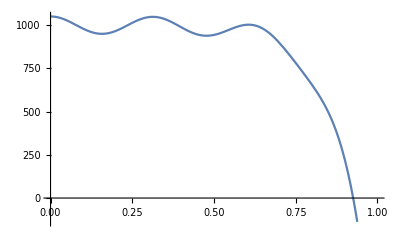

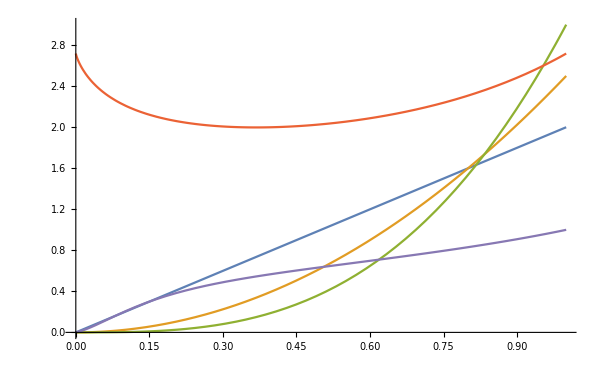

```mathematica
f0[x_]:=2x
f1[x_]:=2.5x*x
f2[x_]:=3x*x*x
f3[x_]:=Exp[x^x]
f4[x_]:=x^(x^(x^(x^x)))
f5[x_]:=1000-0.1Exp[10x]+50Cos[20x]
Plot[f5[x],{x,0,1}]
Plot[{f0[x],f1[x],f2[x],f3[x],f4[x]},{x,0,1},ImageSize->600]
```

```mathematica
x
```

```mathematica
a0=FindRoot[{f0[y]-Integrate[f0[x],{x,0,1}]==0},{y,0.5}]
a1=FindRoot[{f1[y]-Integrate[f1[x],{x,0,1}]==0},{y,0.5}]
a2=FindRoot[{f2[y]-Integrate[f2[x],{x,0,1}]==0},{y,0.5}]
a3=FindRoot[{f3[y]-Integrate[f3[x],{x,0,1}]==0},{y,0.5}]
a4=FindRoot[{f4[y]-Integrate[f4[x],{x,0,1}]==0},{y,0.9}]
a5=FindRoot[{f5[y]-Integrate[f5[x],{x,0,1}]==0},{y,0.9}]
```

{y→0.5}

{y→0.57735}

{y→0.629961}

{y→0.716155}

{y→0.441501}

{y→0.749668}

```mathematica
y/.a0
```

0.5

```mathematica
plotinfo={AxesLabel->{"x","f(x)"},PlotLabel->"f(x)=2x"}
```

{AxesLabel→{x,f(x)},PlotLabel→f(x)=2x}

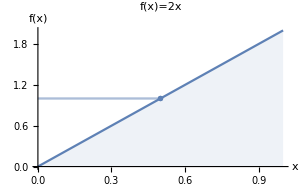

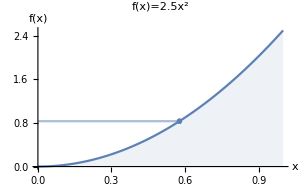

```mathematica
Show[{Plot[{f0[x]},{x,0,1},AxesLabel->{"x","f(x)"},PlotLabel->"f(x)=2x",Filling->Axis,FillingStyle->{Blue,Opacity[0.1]},ImageSize->300],horizontalListPlotFill@ListPlot[{{y/.a0,f0[y/.a0]}}]}]
Show[{Plot[{f1[x]},{x,0,1},AxesLabel->{"x","f(x)"},PlotLabel->"f(x)=2.5x^2",Filling->Axis,FillingStyle->{Blue,Opacity[0.1]},ImageSize->300],horizontalListPlotFill@ListPlot[{{y/.a1,f1[y/.a1]}}]}]
Show[{Plot[{f2[x]},{x,0,1},AxesLabel->{"x","f(x)"},PlotLabel->"f(x)=3x^3",Filling->Axis,FillingStyle->{Blue,Opacity[0.1]},ImageSize->300],horizontalListPlotFill@ListPlot[{{y/.a2,f2[y/.a2]}}]}]
Show[{Plot[{f3[x]},{x,0,1},AxesLabel->{"x","f(x)"},PlotLabel->"f(x)=e^(x^x)",Filling->Axis,FillingStyle->{Blue,Opacity[0.1]},ImageSize->300],horizontalListPlotFill@ListPlot[{{y/.a3,f3[y/.a3]}}]}]
Show[{Plot[{f4[x]},{x,0,1},AxesLabel->{"x","f(x)"},PlotLabel->"f(x)=x^(x^(x^x))",Filling->Axis,FillingStyle->{Blue,Opacity[0.1]},ImageSize->300],horizontalListPlotFill@ListPlot[{{y/.a4,f4[y/.a4]}}]}]
Show[{Plot[{f5[x]},{x,0,1},AxesLabel->{"x","f(x)"},PlotLabel->"f(x)=1000-0.1e^(10  x)+50Cos(x)",Filling->Axis,FillingStyle->{Blue,Opacity[0.1]},ImageSize->300],horizontalListPlotFill@ListPlot[{{y/.a5,f5[y/.a5]}}]}]
1000-0.1Exp[10x]+50Cos[20x]
```

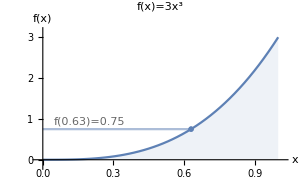

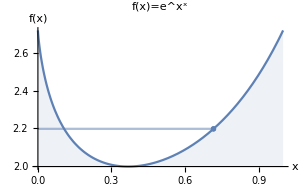

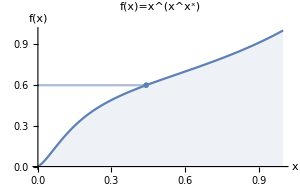

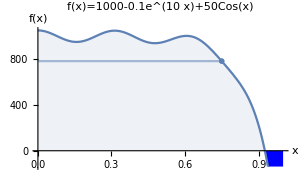

1000-0.1 ⅇ^(10 x)+50 Cos[20 x]

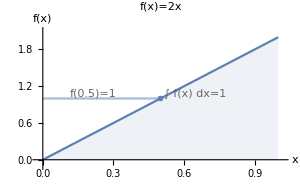

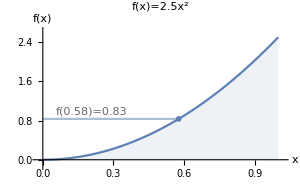

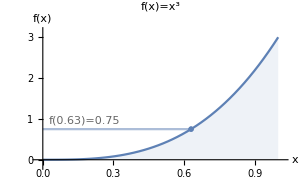

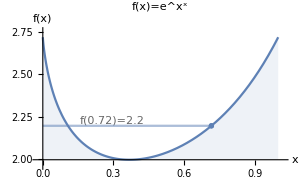

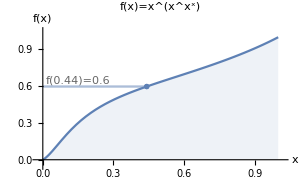

-Graphics-

1000-0.1 ⅇ^(10 x)+50 Cos[20 x]

```mathematica
{a0,Integrate[f0[x],{x,0,1}]}
{a1,Integrate[f1[x],{x,0,1}]}
{a2,Integrate[f2[x],{x,0,1}]}
{a3,Integrate[f3[x],{x,0,1}]//N}
{a4,Integrate[f4[x],{x,0,1}]//N}
{a5,Integrate[f5[x],{x,0,1}]}
f5[0.9]
```

{{y→0.5},1}

{{y→0.57735},0.833333}

{{y→0.629961},3/4}

{{y→0.716155},2.19754}

{{y→0.441501},0.597578}

{{y→0.749668},782.028}

222.707